## Javier Salazar 1001144647

## Project 6.

1.    Classical Gambler's Ruin. 

(a)   Simulate n =10,000 samples and compute the sample average frequency to win  K,  sample average of the game duration
       for K = 40,  i = 5,  p = 18/38  and compare with exact values of  P_i  and  E T.  Animate a sample for K = 20, i = 2.

```mathematica
p=18/38; 
Y:=If[Random[]≤p,1,-1]
n=10000;win=0; K=40; i=5;TotalTime=0;
Do[m=i;T=0;
   While[0<m<K,T=T+1;If[0<m<K,m=m+Y];
 If[m==K,win=win+1]];TotalTime=TotalTime+T,
{n}]
Print["frequency(win K) = ",win/n//N]
Print["P_i = ",(1-((1-p)/p)^i)/(1-((1-p)/p)^K)//N]
Print["average(T) = ", TotalTime/n//N]
Print["E T = ", i/(1-2p)-K/(1-2p)(1-((1-p)/p)^i)/(1-((1-p)/p)^K)//N]
```

frequency(win K) = 0.0123

P_i = 0.0104045

average(T) = 87.297

E T = 87.0926

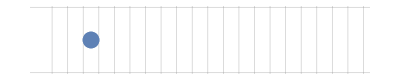

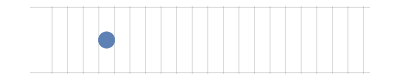

-Graphics-

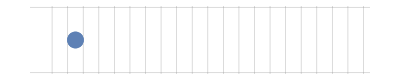

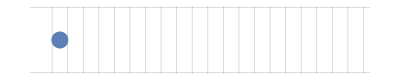

-Graphics-

-Graphics-

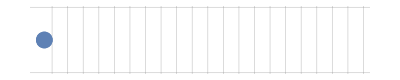

```mathematica
Clear[A];
X:=2RandomInteger[]-1;
i=2; K=20; m=i;Num=0;j=0;

A[0]=ListPlot[{{m-.5,1-.5}},PlotStyle->PointSize[.03],Frame->Automatic,AspectRatio->Automatic,Axes->None,FrameTicks->{{{-.5,0},{0.5,1},{1.5,2},{2.5,3},{3.5,4},{4.5,5},{5.5,6},{6.5,7},{7.5,8},{8.5,9},{9.5,10},{10.5,11},{11.5,12},{12.5,13},{13.5,14},{14.5,15},{15.5,16},{16.5,17},{17.5,18},{18.5,19},{19.5,20}},None},GridLines->{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0,1}},PlotRange->{{-1,20},{0,1}}];

While[0<m<K,
   If[0<m<K,m=m+X];
Print[j=j+1;
A[j]=ListPlot[{{m-.5,1-.5}},PlotStyle->PointSize[.03],Frame->Automatic,AspectRatio->Automatic,Axes->None,FrameTicks->{{{-.5,0},{0.5,1},{1.5,2},{2.5,3},{3.5,4},{4.5,5},{5.5,6},{6.5,7},{7.5,8},{8.5,9},{9.5,10},{10.5,11},{11.5,12},{12.5,13},{13.5,14},{14.5,15},{15.5,16},{16.5,17},{17.5,18},{18.5,19},{19.5,20}},None},GridLines->{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0,1}},PlotRange->{{-1,20},{0,1}}]];
      ];
Num=j;
ListAnimate[Table [A[j],{j,0,Num}],AnimationRate->1]
```

(b)   Consider a slightly unfavorable game with  p = .49 and K =100.  For what initial capital  i  does the game last 
      longest on average ?  Find the corresponding maximum duration of the game.  What is the probability of winning 
      100 in this case?

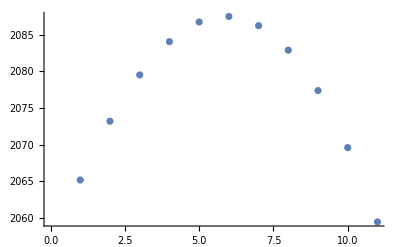

{2065.15,2073.19,2079.51,2084.05,2086.74,2087.49,2086.24,2082.89,2077.37,2069.58,2059.43}

2087.49

0.232501

```mathematica
MeanGameDuration[K_,p_,i_]:=i/(1-2p)-K/(1-2p) (1-((1-p)/p)^i)/(1-((1-p)/p)^K)
ProbabilityWin[K_,p_,i_]:= (1-((1-p)/p)^i)/(1-((1-p)/p)^K)
ListPlot[Table[MeanGameDuration[100,0.49,i],{i,60,70}]]
Table[MeanGameDuration[100,0.49,i],{i,60,70}]
MeanGameDuration[100,0.49,65]//N
ProbabilityWin[100,0.49,65]//N
```

2.   Bold Play Strategy.  Let  K= 2M and p be the probability of winning a single game.  Consider a gambler that follows the 
      the so called bold play strategy defined as follows:
        
      bet  i = the current fortune (to win  i  and have the fortune 2 i  or lose i  and  become bankrupt with  0), whenever  0 < i ≤ M  
      or  bet  K - i  (to win  K - i  and reach the goal of  K  or  lose  K - i  to end up with  2 i - K ), whenever  M < i < 2M.
     
    (a)  Let K = 20.   Find the Markov transition matrix  P  as a function of  p, q  (p + q =1).

```mathematica
Clear[p,q];
P=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0}, {q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, p}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

(b)  Re-label the states  {0→19, 1→0, 2→1, . . . 19→18, 20→20} to obtain a decomposition  P =(Q | R
O | I).

```mathematica
Pnew=RotateLeft[P,1];For[i=1,i<22,i++,Pnew[[i]]=RotateLeft[Pnew[[i]],1]];Pnew//MatrixForm;
```

```mathematica
Q=({{0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, p, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q, 0}});R=({{0, q}, {0, q}, {0, q}, {0, q}, {0, q}, {0, q}, {0, q}, {0, q}, {0, q}, {p, q}, {p, 0}, {p, 0}, {p, 0}, {p, 0}, {p, 0}, {p, 0}, {p, 0}, {p, 0}, {p, 0}});Id=({{{{1, 0}, {0, 1}}}});Θ=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

(c)  Find the matrix U of probabilities to win K or become bankrupt as a function of p and q.

```mathematica
W=Inverse[IdentityMatrix[19]-Q];
U=W.R;U//MatrixForm
```

(-p^5/(-1+p^2 q^2)-(p^5 q)/(-1+p^2 q^2) | q+p q-(p^2 q)/(-1+p^2 q^2)-(p^3 q)/(-1+p^2 q^2)
-p^4/(-1+p^2 q^2)-(p^4 q)/(-1+p^2 q^2) | q-(p q)/(-1+p^2 q^2)-(p^2 q)/(-1+p^2 q^2)
-p^3/(-1+p^2 q^2)-(p^5 q)/(-1+p^2 q^2) | q+p q-(p^2 q^2)/(-1+p^2 q^2)-(p^3 q^2)/(-1+p^2 q^2)
-p^3/(-1+p^2 q^2)-(p^3 q)/(-1+p^2 q^2) | q/(1-p^2 q^2)-(p q)/(-1+p^2 q^2)
p^2 | q+p q
-p^2/(-1+p^2 q^2)-(p^4 q)/(-1+p^2 q^2) | q-(p q^2)/(-1+p^2 q^2)-(p^2 q^2)/(-1+p^2 q^2)
p^2-(p^3 q)/(-1+p^2 q^2)-(p^3 q^2)/(-1+p^2 q^2) | q-(p q^2)/(-1+p^2 q^2)-(p^2 q^4)/(-1+p^2 q^2)
-p^2/(-1+p^2 q^2)-(p^2 q)/(-1+p^2 q^2) | -q/(-1+p^2 q^2)-(p q^3)/(-1+p^2 q^2)
p^2-(p^2 q)/(-1+p^2 q^2)-(p^2 q^2)/(-1+p^2 q^2) | q-(p q^4)/(-1+p^2 q^2)-(p^2 q^4)/(-1+p^2 q^2)
p | q
p-(p^4 q)/(-1+p^2 q^2)-(p^4 q^2)/(-1+p^2 q^2) | q^2-(p q^2)/(-1+p^2 q^2)-(p^2 q^2)/(-1+p^2 q^2)
p/(1-p^2 q^2)-(p^3 q)/(-1+p^2 q^2) | -q^2/(-1+p^2 q^2)-(p q^2)/(-1+p^2 q^2)
p-(p^2 q)/(-1+p^2 q^2)-(p^4 q^2)/(-1+p^2 q^2) | q^2-(p q^3)/(-1+p^2 q^2)-(p^2 q^3)/(-1+p^2 q^2)
p-(p^2 q)/(-1+p^2 q^2)-(p^2 q^2)/(-1+p^2 q^2) | -q^2/(-1+p^2 q^2)-(p q^4)/(-1+p^2 q^2)
p+p q | q^2
p/(1-p^2 q^2)-(p q)/(-1+p^2 q^2) | -q^3/(-1+p^2 q^2)-(p q^3)/(-1+p^2 q^2)
p+p q-(p^2 q^2)/(-1+p^2 q^2)-(p^2 q^3)/(-1+p^2 q^2) | -q^3/(-1+p^2 q^2)-(p q^5)/(-1+p^2 q^2)
p-(p q)/(-1+p^2 q^2)-(p q^2)/(-1+p^2 q^2) | -q^4/(-1+p^2 q^2)-(p q^4)/(-1+p^2 q^2)
p+p q-(p q^2)/(-1+p^2 q^2)-(p q^3)/(-1+p^2 q^2) | -q^5/(-1+p^2 q^2)-(p q^5)/(-1+p^2 q^2))

(d)  Find the matrix  W.1 of the expected time of the game as a function of p and q.

```mathematica
DtoA=Table[Apply[Plus,Table[W[[i,j]],{j,1,7}]],{i,1,7}];
sum=Total[DtoA]
```

6+2 p+1/(1-p^2 q^2)-p/(-1+p^2 q^2)-p^2/(-1+p^2 q^2)-(p q)/(-1+p^2 q^2)-(p^2 q)/(-1+p^2 q^2)-(p^2 q^3)/(-1+p^2 q^2)

(e)  Compare probabilities of  winning  $20 and game duration  for  a classical play  versus  bold play
          for all initial capital  values  i = 1, 2 , . . . , 19   for  p = 18/38, p =1/2 
          
   Hint.  Use  Print[Table[{i, Preg[[i]], Pbold[[i]], MeanGameDuration[20,18/38,i], Dbold[[i]]}, {i, 1, 19}]// TableForm ]

```mathematica
p=18/38;
q=1-p;
Pbold=U[[All,1]];
Print[Table[{i,ProbabilityWin[20,18/38,i]//N,Pbold[[i]]//N,MeanGameDuration[20,18/38,i]//N,Apply[Plus,Table[W[[i,j]],{j,1,7}]]//N},{i,1,19}]//TableForm]
```

1 | 0.0153781 | 0.0388112 | 13.1563 | 1.71293
2 | 0.032465 | 0.0819348 | 25.6633 | 1.50508
3 | 0.0514503 | 0.126711 | 37.4489 | 1.5996
4 | 0.0725452 | 0.172974 | 48.4328 | 1.06627
5 | 0.0959839 | 0.224377 | 58.5261 | 1.
6 | 0.122027 | 0.2675 | 67.6298 | 1.26583
7 | 0.150964 | 0.315415 | 75.6338 | 1.03488
8 | 0.183115 | 0.365166 | 82.4161 | 0.13991
9 | 0.21884 | 0.41657 | 87.8409 | 0.0736371
10 | 0.258533 | 0.473684 | 91.7573 | 0.
11 | 0.302637 | 0.516808 | 93.9978 | 0.792146
12 | 0.351642 | 0.564723 | 94.376 | 0.561197
13 | 0.406091 | 0.614474 | 92.6852 | 0.666226
14 | 0.466591 | 0.665877 | 88.6955 | 0.0736371
15 | 0.533812 | 0.722992 | 82.1513 | 0.
16 | 0.608503 | 0.770907 | 72.7688 | 0.295367
17 | 0.691493 | 0.824146 | 60.2328 | 0.0387564
18 | 0.783703 | 0.879425 | 44.1927 | 0.155456
19 | 0.88616 | 0.936539 | 24.2593 | 0.081819

```mathematica
p=.5
q=1-p;
Pbold=U[[All,1]];
Print[Table[{i,i/20//N,Pbold[[i]]//N,i*(20-i)//N,Apply[Plus,Table[W[[i,j]],{j,1,7}]]//N},{i,1,19}]//TableForm]
```

0.5

1 | 0.05 | 0.05 | 19. | 1.76667
2 | 0.1 | 0.1 | 36. | 1.53333
3 | 0.15 | 0.15 | 51. | 1.63333
4 | 0.2 | 0.2 | 64. | 1.06667
5 | 0.25 | 0.25 | 75. | 1.
6 | 0.3 | 0.3 | 84. | 1.26667
7 | 0.35 | 0.35 | 91. | 1.03333
8 | 0.4 | 0.4 | 96. | 0.133333
9 | 0.45 | 0.45 | 99. | 0.0666667
10 | 0.5 | 0.5 | 100. | 0.
11 | 0.55 | 0.55 | 99. | 0.766667
12 | 0.6 | 0.6 | 96. | 0.533333
13 | 0.65 | 0.65 | 91. | 0.633333
14 | 0.7 | 0.7 | 84. | 0.0666667
15 | 0.75 | 0.75 | 75. | 0.
16 | 0.8 | 0.8 | 64. | 0.266667
17 | 0.85 | 0.85 | 51. | 0.0333333
18 | 0.9 | 0.9 | 36. | 0.133333
19 | 0.95 | 0.95 | 19. | 0.0666667

3.   Mystery Escape.  An 11 story mystery building has 10 doors on each floor.  Each door is labelled UP or DOWN 
      and leads to a staircase to a different floor.  Namely, 11-th floor has 10 doors labelled DOWN, 10-th floor has 9 doors
      labelled DOWN and one labelled UP, . . . , second floor has 1 door labelled DOWN and 9 labelled UP and the first floor 
      has 10 doors labelled UP.  In addition,  all staircases are separated and invisible to each other.   Visitors on the 11-th 
      floor are asked to use stairs to get to the first floor with an idea of using the minimum  number of  doors.  Since the 
      visitors are unfamiliar with the building,  they choose at random the doors labelled DOWN .
       
      Assign states {0, 1, . . . , 10}  to floors 1-11 and consider the Markov chain X_n with  0  being an  absorbing state.
      
(a)   Re-label the states {0→10, 1→0, 2→1, . . . , 10→9} to obtain a decomposition P =(Q | R
O | I).

(b)  How many doors to walk through will it take on average before reaching the 1-st floor.  
       In other words, if  T = number of doors used to reach the ground floor, find  E [T | X_0= 10 ].
       
(c)  Find the answer to (a) and (b) in the case the doors were unlabeled.

```mathematica
P=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 1/3, 1/3, 0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 1/4, 1/4, 1/4, 0, 0, 0, 0, 0, 0, 0}, {1/5, 1/5, 1/5, 1/5, 1/5, 0, 0, 0, 0, 0, 0}, {1/6, 1/6, 1/6, 1/6, 1/6, 1/6, 0, 0, 0, 0, 0}, {1/7, 1/7, 1/7, 1/7, 1/7, 1/7, 1/7, 0, 0, 0, 0}, {1/8, 1/8, 1/8, 1/8, 1/8, 1/8, 1/8, 1/8, 0, 0, 0}, {1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 0, 0}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0}});
Pnew=RotateLeft[P,1];For[i=1,i<12,i++,Pnew[[i]]=RotateLeft[Pnew[[i]],1]];Pnew//MatrixForm;
Q=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 1/3, 0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 1/4, 1/4, 0, 0, 0, 0, 0, 0, 0}, {1/5, 1/5, 1/5, 1/5, 0, 0, 0, 0, 0, 0}, {1/6, 1/6, 1/6, 1/6, 1/6, 0, 0, 0, 0, 0}, {1/7, 1/7, 1/7, 1/7, 1/7, 1/7, 0, 0, 0, 0}, {1/8, 1/8, 1/8, 1/8, 1/8, 1/8, 1/8, 0, 0, 0}, {1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 1/9, 0, 0}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0}});R=({{1}, {1/2}, {1/3}, {1/4}, {1/5}, {1/6}, {1/7}, {1/8}, {1/9}, {1/10}});Id=({{1}});Θ=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
W=Inverse[IdentityMatrix[10]-Q];
W//MatrixForm;
DtoA=Table[Apply[Plus,Table[W[[i,j]],{j,1,10}]],{i,1,10}];
Print["The average number of doors used to reach the ground floor is ", 7381/2520//N]
```

The average number of doors used to reach the ground floor is 2.92897

```mathematica
P=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0}});
Pnew=RotateLeft[P,1];For[i=1,i<12,i++,Pnew[[i]]=RotateLeft[Pnew[[i]],1]];Pnew//MatrixForm
Q=({{0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0, 1/10}, {1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 1/10, 0}});R=({{1/10}, {1/10}, {1/10}, {1/10}, {1/10}, {1/10}, {1/10}, {1/10}, {1/10}, {1/10}});Id=({{1}});Θ=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
W=Inverse[IdentityMatrix[10]-Q];
W//MatrixForm;
DtoA=Table[Apply[Plus,Table[W[[i,j]],{j,1,10}]],{i,1,10}];
Print["The average number of doors used to reach the ground floor is ", 10]
```

(0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10 | 1/10
1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 0 | 1/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The average number of doors used to reach the ground floor is 10